```mathematica
ClearAll["Global'*"];
$PrePrint = MatrixForm;
```

```mathematica
(*Definicje stałych i funkcji*)
G=.01;
H=1;
rho0=1;
ymax=10;
v0[y_]:=(H y)
rho0y[y_]:=(
rho0 + 0.1 Sin[20Pi y / (2 ymax)](**)
)
m[y_]:=(Integrate[rho0y[yy],{yy,0,y}])
xi[y_,t_]:=(y+v0[y]t-2Pi G m[y]t^2)
a[t_]:=1+H t- 2 Pi G rho0 t^2   (*czynnik skali dla rho0y = const*)
xiDy[y_,t_]:=(1+H t-2Pi G rho0y[y] t^2) (*pochodna xi po y*)
xiDt[y_,t_]:=(v0[y]-4Pi G m[y]t) (*pochodna xi po t*)
tCollapse[y_]:=(t/.Solve[xi[y,t]==0,t][[2]])

rhokt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k xi[y,t]],{y,-ymax,ymax}]
)

vkt[k_,t_]:=(
NIntegrate[xiDt[y,t]Exp[-I k xi[y,t]]xiDy[y,t],{y,-ymax,ymax}]
)

rhokScaledt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k / a[t]   xi[y,t]],{y,-ymax,ymax}]
)

rhotxScaled[x_,t_]:=(
rho0y[(x/a[t])/a[t]]Abs[xiDy[(x/a[t])/a[t] ,t]]^(-1)
)

momentumDensityScaled[x_,t_]:=(
rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1) xiDt[(x/a[t]),t]
)
```

```mathematica
(*tmax=Max[t/.{Solve[xi[-ymax,t]==0,t][[2]],Solve[xi[ymax,t]==0,t][[2]]}]; (*Max z czasu zapadania obu końców*)*)
tmax=Re[NMaximize[tCollapse[y],y][[1]]];
tbounce=Max[t/.{Solve[xiDt[-ymax,t]==0,t][[1]],Solve[xiDt[ymax,t]==0,t][[1]]}];
ta0=t/.Solve[{a[t]==0, 0≤t≤tmax},t][[1]]
amax=FindMaximum[a[t],{t,tmax/2}][[1]];
Print["tmax: ",tmax, ", tbounce ",tbounce,", t[a=0] ",ta0,", amax ",amax]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

16.8595

tmax: 18.1065, tbounce 7.95775, t[a=0] 16.8595, amax 4.97887

```mathematica
tstep=.05;
ts=Table[t,{t,0,tmax,tstep}];
k=10;
rhokScaled1=rhokScaledt[k,ts];
(*rhok1=rhokt[k,ts];
vk1=vkt[k,ts];*)
```

```mathematica
(*Wykresy pierwszego modu przeskalowanej transformaty gęstości*)
ListLinePlot[Thread[{ts,Re[rhokScaled1]}],PlotLabels->{"Re"}, PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Im[rhokScaled1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Abs[rhokScaled1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Wyresy pierwszego modu transformat gęstości i prędkości*)
(*tymczasowo nieliczone - trzeba odkomentować rhok1 i vk1*)
ListLinePlot[Thread[{ts,Re[rhok1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhok1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhok1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Re[vk1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
ListLinePlot[Thread[{ts,Im[vk1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
```

```mathematica
(*Wykres xi*)
Plot3D[xi[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

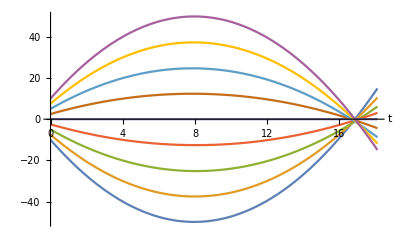

```mathematica
(*Trajektorie*)
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,0,tmax},AxesLabel->Automatic]
```

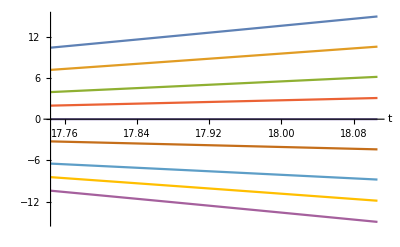

```mathematica
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,tmax*.98,tmax},AxesLabel->Automatic]
```

```mathematica
(*wykres przeskalowanej gęstości: rho[x/a[t],t] dla rho[y]=rho0 *)
rhotxScaled[x_,t_]:=(rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1))
Plot3D[rhotxScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Wykres przeskalowanej gęstości pędu [x/a[t]]*)
Plot3D[momentumDensityScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->{"x","t"}]
```

-Graphics3D-

```mathematica
tMerge[y]:=(
(H + Sqrt[H^2+4 Pi G rho0y[y]])/(4 Pi G rho0y[y])
)
```

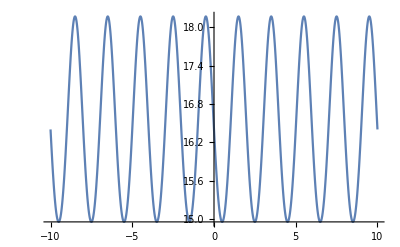

```mathematica
Plot[tMerge[y],{y,-ymax,ymax}]
```

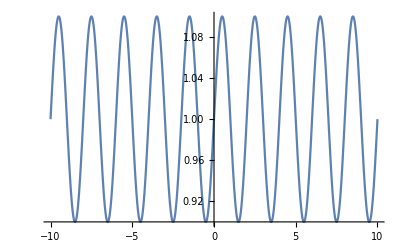

```mathematica
Plot[rho0y[y],{y,-ymax,ymax}]
```

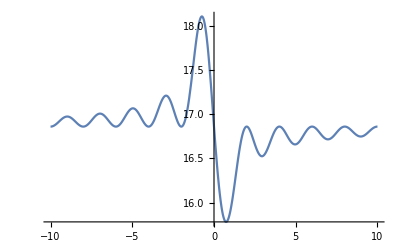

```mathematica
Plot[tCollapse[y],{y,-ymax,ymax},PlotRange->All]
```

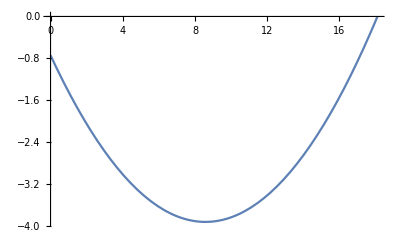

```mathematica
Plot[xi[-0.7420192784331462,t],{t,0,tmax}]
```